```mathematica
(*Author: HKUST,Robotics Institute, William Wu, Wenchao DING*)
(* Key idea of solving the max-min problem:
First, we solve the inner problem by deriving the closed-form solution of \Delta_r 
(dr in the script, i.e., the inflation we need) such that the two inflated balls 
 exactly cover the convex hull of the two original balls. 
This step can be done by expressing the geometry relationship and use the $Solve$ 
 function in mathematica. 

Afterwards, we solve the outer problem using the aforementioned 
 closed- form expression. It then becomes a pure maximization proble which can 
 be solved using $Maximize$ function in mathematica. Alternatively, we can 
 check the second order derivative and first order derivative to verify that the 
\Delta_r is monotonically decreasing with respect to delta (i.e., difference between the 
radius of the two balls, corresponds to \alpha in the paper) for given d and df.
 *)

(* A visualization tool for problem description*)
Manipulate[
r1 = d/2-δ+df;
r2 = d/2 +δ+df;
c0=Circle[{0,0},r1];
c1 = Circle[{d,0},r2]; 
rc0 = Circle[{0,0},r1+dr];
rc1 = Circle[{d,0},r2+dr];
θ = ArcSin[(r2-r1)/d];
p0 = {-r1 Sin[θ],r1 Cos[θ]};
p1 = {d-r2 Sin[θ],r2 Cos[θ]};
p2 = {-r1 Sin[θ],-r1 Cos[θ]};
p3 = {d-r2 Sin[θ],-r2 Cos[θ]};
ans = Solve[{x,y}∈c1&&{x,y}∈c0,{x,y}];
ans2 = Solve[{x,y}∈rc1&&{x,y}∈rc0,{x,y}];
Solve[{x,y}∈rc1&&{x,y}∈rc0&&({x,y}∈InfiniteLine[{p0,p1}]||{x,y}∈InfiniteLine[{p2,p3}]),dr];
Graphics[{{Green,InfiniteLine[{p0,p1}],InfiniteLine[{p2,p3}]},{Blue,c0,c1,rc0,rc1},{Red,PointSize[0.01],Point[{x,y}]/.ans,Point[{x,y}]/.ans2}}]/.{d->cd,δ->cδ,df->cdf,dr->cdr},
{cd,1,10},{cδ,0.0001,cd/2},{cdf,0.01,10},{cdr,0.01,3}
]
```

```mathematica
(* Main program starts here. 
It may need a long time to output results. Just wait for some time.
pls run this block first if any of the block is undefined. *)
```

```mathematica
r1 = d/2-δ+df;
r2 = d/2 +δ+df;
c0=Circle[{0,0},r1];
c1 = Circle[{d,0},r2];
rc0 = Circle[{0,0},r1+dr];
rc1 = Circle[{d,0},r2+dr];
θ = ArcSin[(r2-r1)/d];
p0 = {-r1 Sin[θ],r1 Cos[θ]}
p1 = {d-r2 Sin[θ],r2 Cos[θ]}
p2 = {-r1 Sin[θ],-r1 Cos[θ]}
p3 = {d-r2 Sin[θ],-r2 Cos[θ]}
ans = Solve[d>0&&δ>0&&df>0&&{x,y}∈c1&&{x,y}∈c0,{x,y}];
ans2 = Solve[d>0&&δ>0&&df>0&&{x,y}∈rc1&&{x,y}∈rc0,{x,y}];
(* The following function is to set up the geometry relationship. *)
inner = Solve[d>0&&δ>0&&df>0&&{x,y}∈rc1&&{x,y}∈rc0&&({x,y}∈Line[{p0,p1}]||{x,y}∈Line[{p2,p3}]),{x,y,dr}] 
(* Note that the closed-form solution of \Delta_r (dr) contains four cases 
 after solving the equation. Two of them can be grouped together depending 
 on the valid interval of delta. And the two groups are actually symmetric
 and identical. The resulting solution of \Delta_r is 
 continue (differentiable) everywhere as verified later. *)
```

{(2 δ (-d/2-df+δ))/d,(d/2+df-δ) √(1-(4 δ^2)/d^2)}

{d-(2 δ (d/2+df+δ))/d,(d/2+df+δ) √(1-(4 δ^2)/d^2)}

{(2 δ (-d/2-df+δ))/d,(-d/2-df+δ) √(1-(4 δ^2)/d^2)}

{d-(2 δ (d/2+df+δ))/d,(-d/2-df-δ) √(1-(4 δ^2)/d^2)}

{{x→ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),d>2 √2 √(δ^2)&&df>0&&δ>0],y→ConditionalExpression[-1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),d>2 √2 √(δ^2)&&df>0&&δ>0],dr→ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),d>2 √2 √(δ^2)&&df>0&&δ>0]},{x→ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),d>2 √2 √(δ^2)&&df>0&&δ>0],y→ConditionalExpression[1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),d>2 √2 √(δ^2)&&df>0&&δ>0],dr→ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),d>2 √2 √(δ^2)&&df>0&&δ>0]},{x→ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],y→ConditionalExpression[-1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],dr→ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0]},{x→ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],y→ConditionalExpression[1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],dr→ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0]}}

```mathematica
inner⟦1⟧(* the first case of the closed form solution of [x,y] position and dr (Delta_r)  *)
```

```mathematica
inner⟦2⟧(* the second case of the closed form solution of [x,y] position and dr (Delta_r) *)
```

```mathematica
inner⟦3⟧(* the third case of the closed form solution of  [x,y] position and dr (Delta_r) *)
```

```mathematica
inner⟦4⟧(* the fourth case of the closed form solution of [x,y] position and dr (Delta_r) *)
```

```mathematica
(* we represent \Delta_r w.r.t d, \delta and df. We make use of the observation that 
the extrema only occurs at df = 0. As such we limit d_f
to a very small value in the visualizaton. *)
```

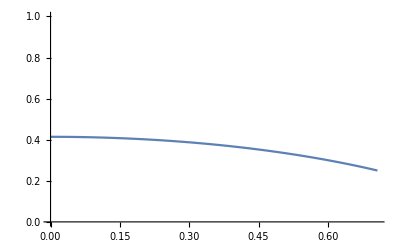
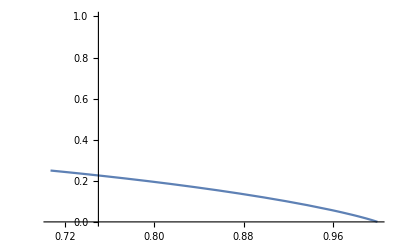
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pdr = dr/.inner;
(* We plot \Delta_r with respect to \delta for visualization.*)
Plot[#,{δ,0.00001,1},PlotRange->{0,1}]&/@(pdr/.{d->2,df->0.00000001})
```

```mathematica
(*The function of \Delta_r w.r.t \delta can be obtained via grouping plot 1 and plot 3 (plot 2 and plot 4 are the other symmetric case). 
In the plot, we can find that when \delta->0 the maximum \Delta_r can be found. *)
(*Here we solve the outer maximization problem using built-in function in Mathematica (numerical method). Note that for delta->0,
  we may encounter some numerical issue, since the two intersections points used in the formulation are reducing to one. *)
```

```mathematica
Maximize[{#,δ<df,δ<0.7}/.d->2,{δ,df}∈Rectangle[{0.0001,0.0001},{1,1}]]&/@Take[pdr,2]
```

{{0.414184,{δ→0.0001,df→0.0001}},{0.414184,{δ→0.0001,df→0.0001}}}

```mathematica
(*   To obtain the maximum \Delta_r theoretically, we calculate the first order and second order derivative for delta in (0, d/2).
  We have the following results:
  1. function Delta_r = f(delta) is continue and differentiable for delta in (0, d/2).
2. first order derivative < 0 for delta in (0, d/2)
 3. As delta ->0, the limit of first order derivative approaches 0
  4. second order derivative < 0 delta in (0, d/2)
  5. function is continue at delta = 0.  

(*1.1 check the continuity at d = 2 √2 delta *)
```

```mathematica
TrueQ[Limit[Take[pdr,{1}]/.{d->2},δ-> √2/2 ,Direction->1]==Limit[Take[pdr,{3}]/.{d->2},δ-> √2/2 ,Direction->-1]]
```

True

```mathematica
(*1.2 check the continuity of first order derivative at d = 2 √2 δ *)
dri11=D[pdr⟦1⟧,δ];
dri31=D[pdr⟦3⟧,δ];
TrueQ[Limit[dri11/.{d->2 ,df-> 0.000001},δ-> √2/2 ,Direction->1]==Limit[dri31/.{d->2,df-> 0.000001},δ-> √2/2 ,Direction->-1]]
```

True

```mathematica
(*2. first order derivative <0 for delta in (0, d/2) *)
test[{ConditionalExpression[x_,cond_]},var_]:=Reduce[x<0,var];
test[{Limit[dri11/.d->2,df->0]},δ]
test[{Limit[dri31/.d->2,df->0]},δ]
```

0<δ<1/(√2)

1/(√2)<δ<1

```mathematica
(*3. As δ ->0, the limit of first order derivative approaches 0*)
Limit[dri11/.{d->2 },δ-> 0 ,Direction->-1]
```

{ConditionalExpression[0,df>0]}

```mathematica
(*4. second order derivative < 0 delta in (0, d/2) *)
dri12 = D[dri11,δ];
test[{Limit[dri12/.d->2,df->0]},δ]
dri32 = D[dri31,δ];
test[{Limit[dri32/.d->2,df->0]},δ]
```

-1/(√2)<δ<0||0<δ<1/(√2)

-1<δ<-1/(√2)||1/(√2)<δ<1

```mathematica
(*5. check the continuity at δ = 0 to make sure there is no invalid extrema.  
  Specifically, for δ = 0, we can easility get Subscript[δ, R] = (√2 - 1)/2×d. 
  On the other hand, for δ -> 0^+, we can use the following to calculate the limit. 
  (δ -> 0^+ and δ -> 0^- are two symmetric cases, and the limits are the same.) 
     Therefore, function Subscript[δ, R] = f(δ)is continue at δ = 0 *)
Limit[Take[pdr,{1}]/.{d->2},δ-> 0 ,Direction->-1]
```

{ConditionalExpression[-1-df+√(2+2 df+df^2),df>0]}